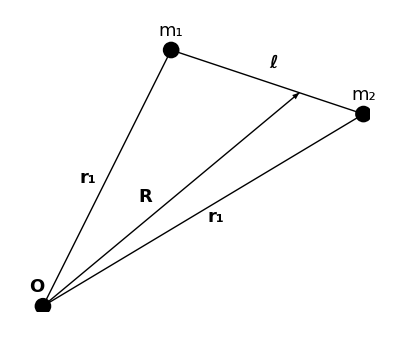

```mathematica
p1={0.2,0.4};
p2={0.5,0.3};
mc=(p1+2*p2)/3;
l=Graphics[{Line[{p1,p2}]}];
ms=Graphics[{PointSize->0.03,Point[p1],Point[p2],Point[{0,0}]}];
vec=Graphics[{Arrow[{{0,0},mc}],Arrow[{{0,0},p1}],Arrow[{{0,0},p2}]}];
texts=Graphics[{
Text[Style["R",18,Bold],{0.16,0.17},FormatType->TraditionalForm],
Text[Style["r_1",18,Bold],{0.07,0.2},FormatType->TraditionalForm],
Text[Style["O",18,Bold],{-0.01,0.03},FormatType->TraditionalForm],
Text[Style["r_1",18,Bold],{0.27,0.14},FormatType->TraditionalForm],
Text[Style["m_1",18],{0.2,0.43},FormatType->TraditionalForm],
Text[Style["m_2",18],{0.5,0.33},FormatType->TraditionalForm],
Text[Style["ℓ",18,Bold],{0.36,0.38},FormatType->StandardForm]
}];
Show[ms,l,vec,texts]
```

r̂

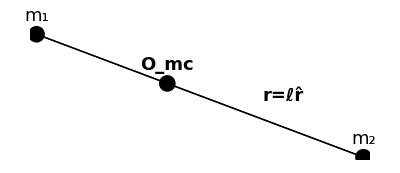

```mathematica
p3={-0.33,0.1};
p4={0.2,-0.1};
mc2=0.6 p3+0.4 p4;
OverHat[r]
l2=Graphics[{Line[{p3,p4}]}];
ms2=Graphics[{PointSize->0.03,Point[p3],Point[p4],Point[mc2]}];
vec=Graphics[{Arrow[{p3,p4}]}];
texts=Graphics[{
Text[Style["O_mc",18,Bold],mc2+{0,0.03},FormatType->TraditionalForm],
Text[Style["m_1",18],p3+{0,0.03},FormatType->TraditionalForm],
Text[Style["m_2",18],p4+{0,0.03},FormatType->TraditionalForm],
Text[Style["r=ℓr̂",18,Bold],{0.07,0.0},FormatType->StandardForm]
}];
Show[ms2,l2,vec,texts]
```